```mathematica
Table[Expand[ a(x)(x-1)+b x],{a,3},{b,3}]//Flatten//DeleteDuplicates
```

{x^2,x+x^2,2 x+x^2,-x+2 x^2,2 x^2,x+2 x^2,-2 x+3 x^2,-x+3 x^2,3 x^2}

```mathematica
Select[Table[Expand[ a(x)(x-1)+b x],{a,1,6},{b,-3,0}]//Flatten//DeleteDuplicates,Last[CoefficientList[#,x]]==1&]
```

{-4 x+x^2,-3 x+x^2,-2 x+x^2,-x+x^2}

```mathematica
CoefficientList[-x+3 x^2,x]
```

{0,-1,3}

```mathematica
Map[CompleteBaseCoeff,DeleteDuplicates[Table[ChromaticPolynomial[allGraphs3[k,"graph"],x],{k,Keys[allGraphs3]}]]]//TableForm
```

0 | 1 | 3 | 1
0 | 0 | 2 | 1
0 | 0 | 1 | 1
0 | 0 | 0 | 1
0 | 0 | 1 | 
0 | 1 | 1 | 
0 | 1 |  |

```mathematica
With[{keys=allGraphs2},
Sort[Map[CompleteBaseCoeff,DeleteDuplicates[Table[ChromaticPolynomial[keys[k,"graph"],x],{k,Keys[keys]}]]]]//TableForm
]
```

0 | 1 | 
0 | 0 | 1
0 | 1 | 1

```mathematica
With[{keys=allGraphs3},
Sort[Map[CompleteBaseCoeff,DeleteDuplicates[Table[ChromaticPolynomial[keys[k,"graph"],x],{k,Keys[keys]}]]]]//TableForm
]
```

0 | 1 |  | 
0 | 0 | 1 | 
0 | 1 | 1 | 
0 | 0 | 0 | 1
0 | 0 | 1 | 1
0 | 0 | 2 | 1
0 | 1 | 3 | 1

```mathematica
With[{keys=allGraphs4},
Sort[Map[CompleteBaseCoeff,DeleteDuplicates[Table[ChromaticPolynomial[keys[k,"graph"],x],{k,Keys[keys]}]]]]//TableForm
]
```

0 | 1 |  |  | 
0 | 0 | 1 |  | 
0 | 1 | 1 |  | 
0 | 0 | 0 | 1 | 
0 | 0 | 1 | 1 | 
0 | 0 | 2 | 1 | 
0 | 1 | 3 | 1 | 
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 2 | 1
0 | 0 | 0 | 3 | 1
0 | 0 | 1 | 2 | 1
0 | 0 | 1 | 3 | 1
0 | 0 | 2 | 4 | 1
0 | 0 | 4 | 5 | 1
0 | 1 | 7 | 6 | 1

```mathematica
With[{keys=allGraphs5},
Sort[Map[CompleteBaseCoeff,DeleteDuplicates[Table[ChromaticPolynomial[keys[k,"graph"],x],{k,Keys[keys]}]]]]//TableForm
]
```

0 | 1 |  |  |  | 
0 | 0 | 1 |  |  | 
0 | 1 | 1 |  |  | 
0 | 0 | 0 | 1 |  | 
0 | 0 | 1 | 1 |  | 
0 | 0 | 2 | 1 |  | 
0 | 1 | 3 | 1 |  | 
0 | 0 | 0 | 0 | 1 | 
0 | 0 | 0 | 1 | 1 | 
0 | 0 | 0 | 2 | 1 | 
0 | 0 | 0 | 3 | 1 | 
0 | 0 | 1 | 2 | 1 | 
0 | 0 | 1 | 3 | 1 | 
0 | 0 | 2 | 4 | 1 | 
0 | 0 | 4 | 5 | 1 | 
0 | 1 | 7 | 6 | 1 | 
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 2 | 1
0 | 0 | 0 | 0 | 3 | 1
0 | 0 | 0 | 0 | 4 | 1
0 | 0 | 0 | 1 | 2 | 1
0 | 0 | 0 | 1 | 3 | 1
0 | 0 | 0 | 2 | 3 | 1
0 | 0 | 0 | 2 | 4 | 1
0 | 0 | 0 | 3 | 4 | 1
0 | 0 | 0 | 3 | 5 | 1
0 | 0 | 0 | 4 | 5 | 1
0 | 0 | 0 | 5 | 5 | 1
0 | 0 | 0 | 6 | 6 | 1
0 | 0 | 0 | 9 | 7 | 1
0 | 0 | 1 | 4 | 4 | 1
0 | 0 | 1 | 5 | 5 | 1
0 | 0 | 1 | 7 | 6 | 1
0 | 0 | 2 | 7 | 6 | 1
0 | 0 | 2 | 10 | 7 | 1
0 | 0 | 4 | 14 | 8 | 1
0 | 0 | 8 | 19 | 9 | 1
0 | 1 | 15 | 25 | 10 | 1

```mathematica
With[{keys=allGraphs6},
Sort[Map[CompleteBaseCoeff,DeleteDuplicates[Table[ChromaticPolynomial[keys[k,"graph"],x],{k,Keys[keys]}]]]]//TableForm
]
```

Keys::invrl: The argument $Failed is not a valid Association or a list of rules.

Table::iterb: Iterator {k,Keys[$Failed]} does not have appropriate bounds.

Table::nliter: Non-list iterator CompleteBaseCoeff[{k,Keys[$Failed]}] at position 2 does not evaluate to a real numeric value.

Table[CompleteBaseCoeff[ChromaticPolynomial[$Failed[k,graph],x]],CompleteBaseCoeff[{k,Keys[$Failed]}]]

```mathematica
DeleteDuplicates[Table[ChromaticPolynomial[allGraphs2[k,"graph"],x],{k,Keys[allGraphs2]}]]
```

{x^2,-x+x^2,x}

```mathematica
Table[allGraphs2[k,"graph"]->ChromaticPolynomial[allGraphs2[k,"graph"],x],{k,Keys[allGraphs2]}]
```

{-Graphics-→x^2,-Graphics-→-x+x^2,-Graphics-→x}

```mathematica
MatrixForm[Table[Expand[ a(x)(x-1)(x-2)+b x(x-1)],{a,1,6},{b,-3,0}],TableHeadings->{Range[6],Range[-3,0]}]
```

( | -3 | -2 | -1 | 0
1 | 5 x-6 x^2+x^3 | 4 x-5 x^2+x^3 | 3 x-4 x^2+x^3 | 2 x-3 x^2+x^3
2 | 7 x-9 x^2+2 x^3 | 6 x-8 x^2+2 x^3 | 5 x-7 x^2+2 x^3 | 4 x-6 x^2+2 x^3
3 | 9 x-12 x^2+3 x^3 | 8 x-11 x^2+3 x^3 | 7 x-10 x^2+3 x^3 | 6 x-9 x^2+3 x^3
4 | 11 x-15 x^2+4 x^3 | 10 x-14 x^2+4 x^3 | 9 x-13 x^2+4 x^3 | 8 x-12 x^2+4 x^3
5 | 13 x-18 x^2+5 x^3 | 12 x-17 x^2+5 x^3 | 11 x-16 x^2+5 x^3 | 10 x-15 x^2+5 x^3
6 | 15 x-21 x^2+6 x^3 | 14 x-20 x^2+6 x^3 | 13 x-19 x^2+6 x^3 | 12 x-18 x^2+6 x^3)

```mathematica
Select[Table[Expand[ a(x)(x-1)(x-2)+b x(x-1)],{a,1,6},{b,-3,0}]//Flatten//DeleteDuplicates,Last[CoefficientList[#,x]]==1&]
```

```mathematica
{5 x-6 x^2+x^3,4 x-5 x^2+x^3,3 x-4 x^2+x^3,2 x-3 x^2+x^3}
```

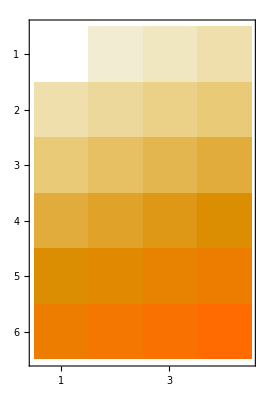

```mathematica
MatrixPlot[Table[Factor[ a(x)(x-1)+b x]/.x->4,{a,1,6},{b,-3,0}]]
```